# Precipitation Predictability over Extended Lead Time for West Coast United States

BX Pan
2017.10.22

## Background

The Quiet Revolution of Numerical Weather Prediction

```mathematica
ECMWF=Labeled[ImageResize[Import["/Users/lambda/Documents/Research/3_S2SEvaluation/Refer/RevolutionOfECMWF.png"],
		1000],
	"Fig1. Predictability(Correlation) of Extratropical 500hpa GPH from ECMWF,  Bauer, etc. Nature, 2015",Bottom]
```

-Graphics-Fig1. Predictability(Correlation) of Extratropical 500hpa GPH from ECMWF,  Bauer, etc. Nature, 2015

```mathematica
NCEP=Labeled[ImageResize[Import["/Users/lambda/Documents/Research/3_S2SEvaluation/Refer/RevolutionOfNCEP.png"],
		1000],
	"Fig2. Predictability(Mean Error) of North America 500hpa GPH from NCEP,  NCEP Central Operations, March, 2016",Bottom]
```

-Graphics-Fig2. Predictability(Mean Error) of North America 500hpa GPH from NCEP,  NCEP Central Operations, March, 2016

Could “S2S forecasts be as widely used a decade from now as weather forecasts are today”?

Stretch the lead time of weather timescale models forward and climate models backward.

The Ongoing Inquiry of the Foundation of “Climate Projection”

```mathematica
TableForm[{{"Initial Value Problem","Deterministic"},
           {"Boundary Value Problem","Proabilisitc"}},
          TableHeadings->{{"Weather Forecast","Climate Prediction"},None}]
```

Weather Forecast | Initial Value Problem | Deterministic
Climate Prediction | Boundary Value Problem | Proabilisitc

A deterministic system could be unpredictable:

Is the earth’s weather system ergodic? (more illustrations should be added here)

If it was ergodic, will an imperfect model be a valid predictor for the climate’s statistical features?

The Emerging Demand for Accurate and Extended Quantitative Precipitation Forecast(QPF)

```mathematica
Labeled[ImageResize[Import["/Users/lambda/Documents/Research/3_S2SEvaluation/Refer/DemandForS2S.png"],1000],
	 "Demand For Accurate and Extended QPF, modified from the Earth System Prediction Capability Office.",Bottom]
```

-Graphics-Demand For Accurate and Extended QPF, modified from the Earth System Prediction Capability Office.

Predictability for extratropical and tropical areas are different, due to different precipitation mechanisms.

```mathematica
ImageResize[xkcdConvert[ListLinePlot[{{{1,0.86},{2,0.85},{3,0.75},{4,0.7},{5,0.65},{7,0.5},{10,0.3},{12,0.13},{14,0.13},{20,0.135},{30,0.2}},
              {{1,0.7},{2,0.65},{4,0.5},{7,0.45},{14,0.4},{20,0.42},{30,0.43}}},
              PlotStyle->{Blue,Red},
              Frame->True,
              Ticks->None,
              FrameLabel->{"Forecast Leading Days","Predictability"},
              Epilog -> 
   xkcdLabel /@ {{"Extratropic", {3, 0.75}, {1, 0}}, {"Tropic", {4, 0.5}, {0, -0.3}}}]],700]
```

-Graphics-

Extratropical predictability is mostly derived from synoptic-scale atmospheric dynamics

Tropical predictability is primarily derived from the response of moist convection to
slowly varying forcing such as from ENSO.

Subseasonal to Seasonal Prediction Project (2013-2018)

## Opportunities and Challenges

sampling effect?

California

38 million people(12% total US population)
9 million irrigated acres farm that lead the nation in production
demand for hydroelectricity from the state’s 13765 MW of capacity

#### California Department of Water Resources’s forecast of total April-July river runoff. water-year based indices

USDA Natural Resources Conservation Service in partnership with NOAA/National Weather Service

Snowpack

Oregon

Washington

Capacity to Predict MJO (average gain of 1 day of prediction skill per year)

Teleconnection between MJO and extratropics

North Atlantic Oscillation Index

2m temperature anormalies

Tropical Cyclones

Extratropical Storm Tracks

## Research Question

Where we are now in the respect of S2S predictability?

Dynamical Methods

Statistical Methods

## Literature Review

The most important aspect of the challenge is the chaotic nature of weather and climate predictability that needs to be characterized with probabilistic information.

## Data

S2S, sub-seasonal to seasonal prediction project, is a WWRP/THORPEX-WCRP joint research project established to improve forecast skill and understanding on the sub-seasonal to seasonal time scale, and promote its uptake by operational centres and exploitation by the applications community.

```mathematica
TableForm[{{"","Ocean Model","Sea Ice Model","Landsurface Model",""},
           {"BoM","ACOM2 (Schiller and Godfrey 2003)","",""},
           {"BoM","ACOM2 (Schiller and Godfrey 2003)","",""}}]
```

Initial conditions and perturbations

Data assimilation method for control analysis: Nudging from 4dVar reanalysis
Resolution of model used to generate Control Analysis: T47
Ensemble initial perturbation strategy: Coupled bred vectors
Horizontal and vertical resolution of perturbations:  T47
Perturbations in +/- pairs: no

```mathematica
datasets=Block[{model,primary,size,frequency},
	SetDirectory["/Users/lambda/Documents/Research/3_S2SEvaluation/Data"];
	models=Select[FileNames[],StringFreeQ[#,"."]&];
	primary={
		{Green,"BoM",LinguisticAssistant},    
		{Red,"CMA",LinguisticAssistant},  
		{Purple,"StyleBox[\"ECCC\",FontWeight->\"Bold\"]",LinguisticAssistant}, 
		{Gray,"StyleBox[\"ECMWF\",FontWeight->\"Bold\"]",LinguisticAssistant},
		{Magenta,"StyleBox[\"HMCR\",FontWeight->\"Bold\"]",LinguisticAssistant},   
		{Yellow, "ISAC-CNR",LinguisticAssistant}, 
		{LightPurple,"JMA", LinguisticAssistant},
		{Brown, "StyleBox[\"KMA\",FontWeight->\"Bold\"]",LinguisticAssistant},  
		{Cyan,"Météo-France",LinguisticAssistant},  
		{Blue,"NCEP",LinguisticAssistant},
		{Orange, "StyleBox[\"UKMO\",FontWeight->\"Bold\"]",LinguisticAssistant}};
	size=Map[Block[{data=Import["/Users/lambda/Documents/Research/3_S2SEvaluation/Data/"<>#<>"/"<>#<>".mx"]},
		Dimensions[data[[1]]]][[{1,3}]]&,models];
	frequency=Block[{time,f,e},
		time=Map[Import["/Users/lambda/Documents/Research/3_S2SEvaluation/Data/"<>#<>"/"<>#<>"_control_time.mx"]&,models];
		f=Map[Round[#[[1]],0.1]&,Map[(DateDifference[#[[1]],#[[-1]]])/(Length[#]+0.0)&,time]];
		e=Map[{#[[1,1]],#[[-1,1]]}&,time];
		Map[If[#[[1]]<1.01,
		"Every day from "<>ToString[#[[2,1]]]<>" to "<>ToString[#[[2,2]]],
		"Every "<>ToString[#[[1]]]<>" days from "<>ToString[#[[2,1]]]<>" to "<>ToString[#[[2,2]]]]&,Transpose[{f,e}]]];
	Map[Flatten,Transpose[{primary,size,frequency}]]];
label=TableForm[Map[Flatten[{#[[1]],#[[2]]<>"("<>ToString[#[[3]][[2]]]<>")",#[[4;;]]}]&,datasets],
	TableHeadings->{None,{"","Model","Ensemble Size","Extension(day)","Hincast Frequency"}},
	TableAlignments->Left];
Labeled[Show[GeoRegionValuePlot[Map[#[[3]]->#[[1]]&,datasets]],
	  GeoRegionValuePlot[Map[#[[3]]->#[[1]]&,datasets[[{6,9,11}]]]],ImageSize->1160],
	  label,Bottom]
(*Export["/Users/lambda/Documents/Research/3_S2SEvaluation/Results/fig1_dataset.pdf",%];*)
```

-Graphics- | Model | Ensemble Size | Extension(day) | Hincast Frequency
RGBColor[0, 1, 0] | BoM(Australia) | 33 | 62 | Every 5.1 days from 1981 to 2013
RGBColor[1, 0, 0] | CMA(China) | 4 | 60 | Every day from 1994 to 2014
RGBColor[0.5, 0, 0.5] | ECCC(Canada) | 4 | 32 | Every 4.1 days from 1995 to 2014
GrayLevel[0.5] | ECMWF(Europe) | 11 | 46 | Every 2.6 days from 1995 to 2016
RGBColor[1, 0, 1] | HMCR(Russia) | 10 | 61 | Every 2.9 days from 1985 to 2010
RGBColor[1, 1, 0] | ISAC-CNR(Italy) | 1 | 31 | Every 5. days from 1981 to 2010
RGBColor[0.94, 0.88, 0.94] | JMA(Japan) | 5 | 34 | Every 10.1 days from 1981 to 2010
RGBColor[0.6, 0.4, 0.2] | KMA(SouthKorea) | 3 | 60 | Every 10.9 days from 1991 to 2010
RGBColor[0, 1, 1] | Météo-France(France) | 15 | 61 | Every 15.2 days from 1993 to 2014
RGBColor[0, 0, 1] | NCEP(UnitedStates) | 4 | 44 | Every day from 1999 to 2010
RGBColor[1, 0.5, 0] | UKMO(UnitedKingdom) | 3 | 60 | Every 7.6 days from 1993 to 2015

## Skill Metric

Deterministic

Probabilistic

## Evaluation Results

Correlation

```mathematica
image=Import["/Users/lambda/Documents/Research/3_S2SEvaluation/Git/Result/fig2_Correlation.pdf"][[1]];
ImageResize[image,1300]
```

-Graphics-

RMSE

#### Raw

```mathematica
image=Import["/Users/lambda/Documents/Research/3_S2SEvaluation/Git/Result/fig3_RMSE.pdf"][[1]];
ImageResize[image,1300]
```

-Graphics-

#### Linear Corrected

```mathematica
image=Import["/Users/lambda/Documents/Research/3_S2SEvaluation/Git/Result/fig4_LinearRMSE.pdf"][[1]];
ImageResize[image,1300]
```

-Graphics-

NSE

#### Raw

```mathematica
image=Import["/Users/lambda/Documents/Research/3_S2SEvaluation/Git/Result/fig5_NSE.pdf"][[1]];
ImageResize[image,1300]
```

-Graphics-

#### Linear Corrected

```mathematica
image=Import["/Users/lambda/Documents/Research/3_S2SEvaluation/Git/Result/fig6_LinearNSE.pdf"][[1]];
ImageResize[image,1300]
```

-Graphics-

ROC

#### Raw

#### Linear Corrected

## Prediction Opportunity

On the Long Term Prediction of Chaotic System

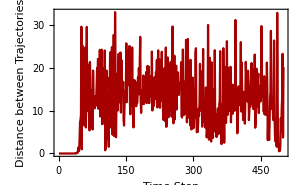
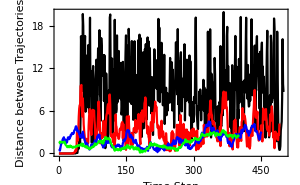
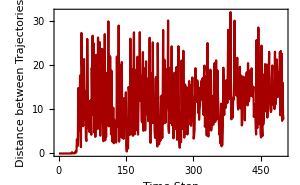
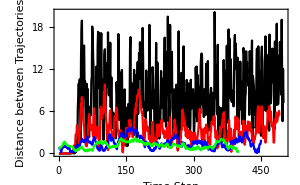
| Trajectory_1 | Trajectory_2 | L2 Distance | L2 Distance of Temporal Mean
{0, 1, 1} | -Graphics3D- | -Graphics3D- | -Graphics- | -Graphics-
{-10, 10, 10} | -Graphics3D- | -Graphics3D- | -Graphics- | -Graphics-Lorenz System Simulations by Pertubating y_0 of 1/10000000000

```mathematica
scale=ImageResize[ImageCrop[-Graphics-],800];
Labeled[scale,"Time series depicting variations of weather/climate, 
Next Generation Earth System Prediction: Strategies for Subseasonal to Seasonal Forecasts. Washington, DC: The National Academies Press. doi: 10.17226/21873.",Bottom]
```

-Graphics-Time series depicting variations of weather/climate, 
Next Generation Earth System Prediction: Strategies for Subseasonal to Seasonal Forecasts. Washington, DC: The National Academies Press. doi: 10.17226/21873.

Climate system undergoes different scenarios through its evolution. The slowly varying components can provide information for extended forecast. When dynamical models are initialized at certain phase of these  phenomena, the model forecasts match observations with more fidelity than the neutral phases. These intervals are named as forecast windows and believed to bring prediction opportunities.

## Examples

ENSO

```mathematica
impactLaNina=ImageCrop[-Graphics-];
impactElNino=ImageCrop[-Graphics-];
enso=ImageCrop[-Graphics-];
GraphicsRow[{ImageResize[enso,500],ImageResize[impactLaNina,500],ImageResize[impactElNino,500]},ImageSize->Full]
```

-Graphics-

MJO

```mathematica
mjo=ImageCrop[-Graphics-];
ImageResize[mjo,1000]
```

-Graphics-

-Graphics- | -Graphics-"Meet the MJO, By Jon Gottschalck, NOAA Climate Prediction Center with Andrea Ray, WWA

Stratospheric Sudden Warming

When initialized at the onset date of stratospheric sudden warmings, the model forecasts faithfully reproduce the observed mean tropospheric conditions in the months following the stratospheric sudden warmings. Compared with an equivalent set of forecasts that are not initialized during stratospheric sudden warmings, we document enhanced forecast skill for atmospheric circulation patterns, surface temperatures over northern Russia and eastern Canada and North Atlantic precipitation. We suggest that seasonal forecast systems initialized during stratospheric sudden warmings are likely to yield significantly greater forecast skill in some regions.
e identified
the stratosphere as an untapped source of enhanced seasonal
predictability.

Seasonal forecast systems based on dynamical models are able to
capture the average tropospheric state following SSWs to some
extent12, but it is not evident that this is associated with a detectable
increase in forecast skill of surface weather13. Here we demonstrate
that a dynamical forecast system initialized at the time of a SSW
is able to predict the mean tropospheric circulation response in
the following months

The dynamical forecast system in this study employs the Canadian
Middle Atmosphere Model14. Retrospective forecasts (also
known as hindcasts) are initialized at 20 SSW dates between
1970 and 2009 (hereafter referred to as the SSW forecasts), each
consisting of 10 ensemble members.

Methodology

Cluster prediction results according to climate conditions and compare with long-run/neutral conditions

## Seeking Forecast windows ⟶ MJO

Parameterization of MJO

1, filter OLR to retain only frequencies associated with the MJO. 
2, Filtered OLR between 208S and 208N is then subjected to a standard covariance matrix EOF analysis that retains the local variance of the OLR fluctuations.

```mathematica
MJO=Import["/Users/lambda/Documents/Research/3_S2SEvaluation/MJO/OMI","Table"];
```

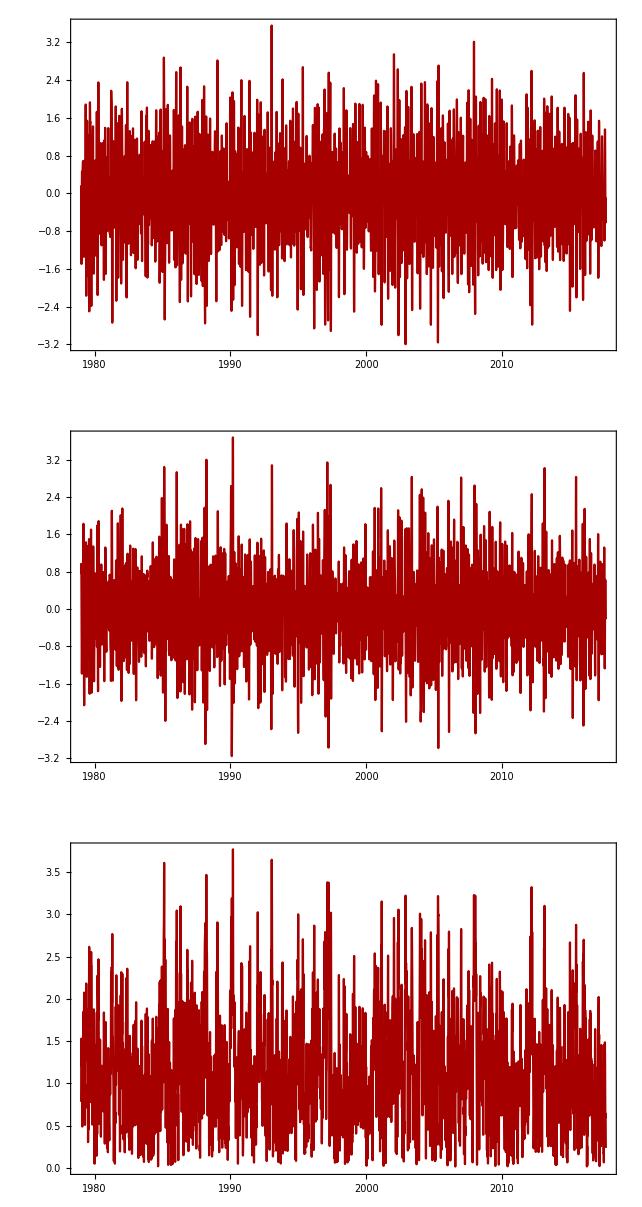

```mathematica
GraphicsColumn[{DateListPlot[TimeSeries[MJO[[;;,5]],{{1979,1,1}}],ImageSize->600],
                DateListPlot[TimeSeries[MJO[[;;,6]],{{1979,1,1}}],ImageSize->600],
                DateListPlot[TimeSeries[MJO[[;;,7]],{{1979,1,1}}],ImageSize->600]}]
```

## Seeking Forecast windows ⟶ ENSO

Given that:

GCMs can capture/predict ENSO

```mathematica
nino34=-Graphics-;
nino12=-Graphics-;
nino4=-Graphics-;
nino3=-Graphics-;
GraphicsGrid[ArrayReshape[Map[ImageResize[ImageCrop[#],500]&,{nino12,nino3,nino34,nino4}],
	{2,2}],ImageSize->1200]
```

-Graphics-

It’s believed that under different phases of ENSO, precipitation for the West Coast United States would be distinct. Specifically:

```mathematica
ENSO=-Graphics-;
LANINA=-Graphics-;
GraphicsRow[Map[ImageResize[ImageCrop[#],500]&,{ENSO,LANINA}],ImageSize->Full]
```

-Graphics-

DIfference from average (1981-2010) winter precipitation (December-February) in each U.S. climate division during strong (dark gray bar), moderate (medium gray), and weak (light gray) El Niño/La Nina events since 1950. Years are ranked based on the maximum seasonal ONI index value observed. During strong El Niño events, the Gulf Coast and Southeast are consistently wetter than average. Maps by NOAA Climate.gov, based on NCDC climate division data provided by the Physical Sciences Division at NOAA ESRL.

We can deduce the following hypotheses:

GCMs can capture/predict ENSO

Implementation

DESCRIPTION: Warm (red) and cold (blue) periods based on a threshold of +/- 0.5oC for the Oceanic Niño Index (ONI) [3 month running mean of ERSST.v5 SST anomalies in the Niño 3.4 region (5oN-5oS, 120o-170oW)], based on centered 30-year base periods updated every 5 years.

```mathematica
Cluster[dataset_,threshould_:0.5]:=Block[{index,IndexTime,time,rIndex,clusters},
	index=Import["/Users/lambda/Documents/Research/3_S2SEvaluation/ClimateIndex/ENSO/NINO34.nc",
		{"Datasets","NINO34"}];
	IndexTime=Map[DatePlus[{1960,1,1},{#,"Month"}][[1;;2]]&,Import["/Users/lambda/Documents/Research/3_S2SEvaluation/ClimateIndex/ENSO/NINO34.nc",
		{"Datasets","T"}]];
	time=Import["/Users/lambda/Documents/Research/3_S2SEvaluation/Data/"<>dataset<>"/"<>dataset<>"_control_time.mx"];
	time=Select[time,Or[#[[2]]>=10,#[[2]]≤3]&];
	rIndex=Map[index[[Position[IndexTime,#[[1;;2]]][[1,1]]]]&,time];
	clusters={Position[rIndex,_?(#>threshould&)][[;;,1]],
			  Position[rIndex,_?(#<-threshould&)][[;;,1]],
			  Position[rIndex,_?(And[#<threshould,#>-threshould]&)][[;;,1]]};
	clusters]
```

```mathematica
Evaluation[dataset_,skill_:Correlation,cluster_]:=
Block[{SCAsimu,NCAsimu,ORsimu,WAsimu,
	   SCAobser,NCAobser,ORobser,WAobser,
	   mSCAsimu,mNCAsimu,mORsimu,mWAsimu,
	   iSCAsimu,iSCAobser,iNCAsimu,iNCAobser,
	   imSCAsimu,imNCAsimu,imORsimu,imWAsimu,
	   iORsimu,iORobser,iWAsimu,iWAobser,
	   GridDaily,GridInterval,RegionalDaily,RegionalInterval,
	   int},

{{{SCAsimu,NCAsimu,ORsimu,WAsimu},{SCAobser,NCAobser,ORobser,WAobser}},
	 {{iSCAsimu,iNCAsimu,iORsimu,iWAsimu},{iSCAobser,iNCAobser,iORobser,iWAobser}}}=
	 Import[main<>"Data/"<>dataset<>"/"<>dataset<>"_dg.mx"];
{SCAobser,NCAobser,ORobser,WAobser}=Map[#[[cluster,;;,;;]]&,{SCAobser,NCAobser,ORobser,WAobser}];	 
{SCAsimu,NCAsimu,ORsimu,WAsimu}=Map[#[[;;,cluster,;;,;;]]&,{SCAsimu,NCAsimu,ORsimu,WAsimu}];

{iSCAobser,iNCAobser,iORobser,iWAobser}=Map[Map[If[Length[#]>0,#[[cluster,;;]],#]&,#]&,{iSCAobser,iNCAobser,iORobser,iWAobser}];
{iSCAsimu,iNCAsimu,iORsimu,iWAsimu}=Map[#[[;;,;;,cluster,;;]]&,{iSCAsimu,iNCAsimu,iORsimu,iWAsimu}];


{mSCAsimu,mNCAsimu,mORsimu,mWAsimu}=Map[Mean,{SCAsimu,NCAsimu,ORsimu,WAsimu}];
{imSCAsimu,imNCAsimu,imORsimu,imWAsimu}=Map[Map[If[Length[#]>0,Mean[#],0]&,#]&,{iSCAsimu,iNCAsimu,iORsimu,iWAsimu}];

	
GridDaily={Mean[Table[Table[skill[mSCAsimu[[;;,extension,grid]],SCAobser[[;;,extension,grid]]],
		{extension,Dimensions[SCAobser][[2]]}],{grid,Dimensions[SCAobser][[3]]}]],
		   Mean[Table[Table[skill[mNCAsimu[[;;,extension,grid]],NCAobser[[;;,extension,grid]]],
		{extension,Dimensions[NCAobser][[2]]}],{grid,Dimensions[NCAobser][[3]]}]],
		   Mean[Table[Table[skill[mORsimu[[;;,extension,grid]],ORobser[[;;,extension,grid]]],
		{extension,Dimensions[ORobser][[2]]}],{grid,Dimensions[ORobser][[3]]}]],
		   Mean[Table[Table[skill[mWAsimu[[;;,extension,grid]],WAobser[[;;,extension,grid]]],
		{extension,Dimensions[WAobser][[2]]}],{grid,Dimensions[WAobser][[3]]}]]};

RegionalDaily={Table[skill[Mean[Transpose[Map[Transpose,mSCAsimu]]][[;;,day]],
			  Mean[Transpose[Map[Transpose,SCAobser]]][[;;,day]]],{day,Dimensions[SCAobser][[-2]]}],
			   Table[skill[Mean[Transpose[Map[Transpose,mNCAsimu]]][[;;,day]],
			  Mean[Transpose[Map[Transpose,NCAobser]]][[;;,day]]],{day,Dimensions[NCAobser][[-2]]}],
			   Table[skill[Mean[Transpose[Map[Transpose,mORsimu]]][[;;,day]],
			  Mean[Transpose[Map[Transpose,ORobser]]][[;;,day]]],{day,Dimensions[ORobser][[-2]]}],
			   Table[skill[Mean[Transpose[Map[Transpose,mWAsimu]]][[;;,day]],
			  Mean[Transpose[Map[Transpose,WAobser]]][[;;,day]]],{day,Dimensions[WAobser][[-2]]}]};
	
GridInterval={Table[If[Length[imSCAsimu[[i]]]==0,Null,
				Mean[Table[skill[imSCAsimu[[i]][[;;,grid]],iSCAobser[[i]][[;;,grid]]],{grid,Dimensions[iSCAobser[[i]]][[-1]]}]]],
				{i,Length[imSCAsimu]}],
			  Table[If[Length[imNCAsimu[[i]]]==0,Null,
				Mean[Table[skill[imNCAsimu[[i]][[;;,grid]],iNCAobser[[i]][[;;,grid]]],{grid,Dimensions[iNCAobser[[i]]][[-1]]}]]],
				{i,Length[imNCAsimu]}],
			  Table[If[Length[imORsimu[[i]]]==0,Null,
				Mean[Table[skill[imORsimu[[i]][[;;,grid]],iORobser[[i]][[;;,grid]]],{grid,Dimensions[iORobser[[i]]][[-1]]}]]],
				{i,Length[imORsimu]}],
			  Table[If[Length[imWAsimu[[i]]]==0,Null,
				Mean[Table[skill[imWAsimu[[i]][[;;,grid]],iWAobser[[i]][[;;,grid]]],{grid,Dimensions[iWAobser[[i]]][[-1]]}]]],
				{i,Length[imWAsimu]}]};

RegionalInterval={Table[If[Length[imSCAsimu[[i]]]==0,Null,
		skill[Mean[Transpose[imSCAsimu[[i]]]],Mean[Transpose[iSCAobser[[i]]]]]],{i,Length[imSCAsimu]}],
				 Table[If[Length[imNCAsimu[[i]]]==0,Null,
		skill[Mean[Transpose[imNCAsimu[[i]]]],Mean[Transpose[iNCAobser[[i]]]]]],{i,Length[imNCAsimu]}],
				 Table[If[Length[imNCAsimu[[i]]]==0,Null,
		skill[Mean[Transpose[imORsimu[[i]]]],Mean[Transpose[iORobser[[i]]]]]],{i,Length[imORsimu]}],
				 Table[If[Length[imWAsimu[[i]]]==0,Null,
		skill[Mean[Transpose[imWAsimu[[i]]]],Mean[Transpose[iWAobser[[i]]]]]],{i,Length[imWAsimu]}]};
	
{GridDaily,RegionalDaily,GridInterval,RegionalInterval}];
```

```mathematica
models
```

{BoM,CMA,ECCC,ECMWF,HCMR,ISACCNR,JMA,KMA,MeteoFrance,NCEP,UKMO}

```mathematica
Visualize[dataset_]:=Block[{cluster,ElNinoBoM,LaNinaBoM,NeutralBoM,label},
label=SwatchLegend[{Blue,Red,Gray},{"El Niño","La Niña","Neutral"},
	LabelStyle->{FontSize->25},
	LegendMarkerSize->25,
	LegendLayout->"Row"];
clusters=Cluster[dataset];
ElNinoBoM=Evaluation[dataset,Correlation,clusters[[1]]];
LaNinaBoM=Evaluation[dataset,Correlation,clusters[[2]]];
NeutralBoM=Evaluation[dataset,Correlation,clusters[[3]]];
Labeled[TableForm[Table[Block[{griddaily,regionaldaily,gridinterval,regionalinterval},
griddaily=ListLinePlot[{ElNinoBoM[[1,region]],LaNinaBoM[[1,region]],NeutralBoM[[1,region]]},
	Frame->True,
	BaseStyle->15,
	ImageSize->300,
	PlotRange->Full,
	FrameLabel->{"Forecast Leading Day","Correlation"},
	PlotStyle->{Red,Blue,Gray}];
regionaldaily=ListLinePlot[{ElNinoBoM[[2,region]],LaNinaBoM[[2,region]],NeutralBoM[[2,region]]},
	Frame->True,
	BaseStyle->15,
	ImageSize->300,
	PlotRange->Full,
	FrameLabel->{"Forecast Leading Day","Correlation"},
	PlotStyle->{Red,Blue,Gray}];
gridinterval=BarChart[Transpose[{ElNinoBoM[[3,region]],
								LaNinaBoM[[3,region]],
								NeutralBoM[[3,region]]}],
	BaseStyle->10,
	BarSpacing->{0,4.},
	ChartStyle->{Red,Blue,Gray},
	ChartLabels->{{"1d1d","2d2d","4d4d","1w1w","2w2w","3w3w","4w4w"},None},
	Frame->True,
	FrameLabel->{"Forecast Interval","Correlation"},
	ImageSize->300];
regionalinterval=BarChart[Transpose[{ElNinoBoM[[4,region]],
								LaNinaBoM[[4,region]],
								NeutralBoM[[4,region]]}],
	BaseStyle->10,
	BarSpacing->{0,4.},
	ChartStyle->{Red,Blue,Gray},
	ChartLabels->{{"1d1d","2d2d","4d4d","1w1w","2w2w","3w3w","4w4w"},None},
	Frame->True,
	FrameLabel->{"Forecast Interval","Correlation"},
	ImageSize->300];
{griddaily,regionaldaily,gridinterval,regionalinterval}],{region,4}],
	TableSpacing->{-10,-20},
	TableHeadings->{{"SCA","NCA","OR","WA"}, {"Grid Daily Scale","Regional Daily Scale","Grid Interval Scale","Regional Interval Scale"}},
	TableAlignments->Center
],label,Bottom]]
```

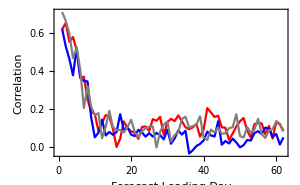
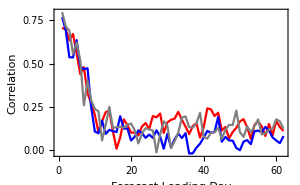
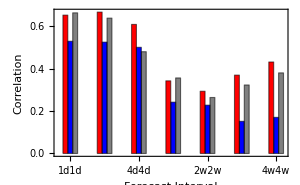
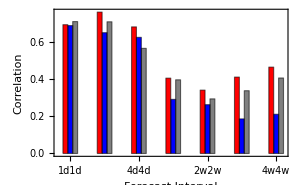
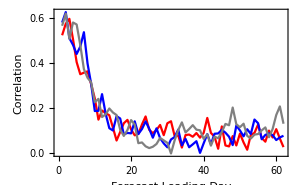
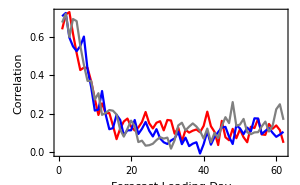
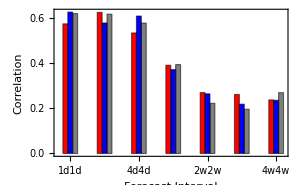
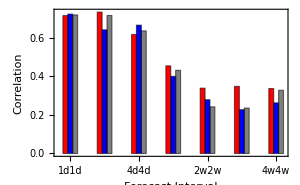
| Grid Daily Scale | Regional Daily Scale | Grid Interval Scale | Regional Interval Scale
SCA | -Graphics- | -Graphics- | -Graphics- | -Graphics-
NCA | -Graphics- | -Graphics- | -Graphics- | -Graphics-
OR | -Graphics- | -Graphics- | -Graphics- | -Graphics-
WA | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Visualize["BoM"]
```

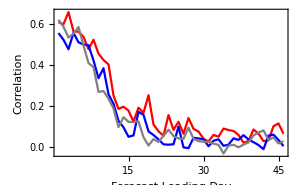
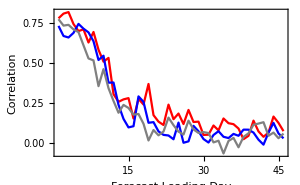
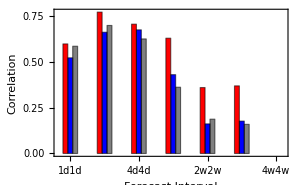
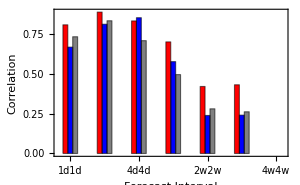
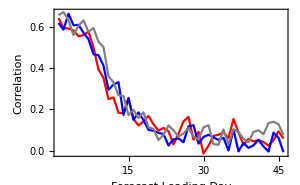
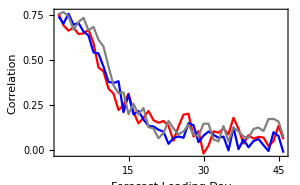
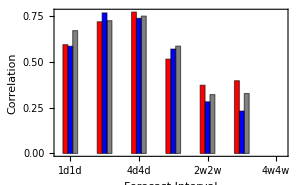
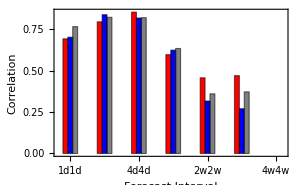
| Grid Daily Scale | Regional Daily Scale | Grid Interval Scale | Regional Interval Scale
SCA | -Graphics- | -Graphics- | -Graphics- | -Graphics-
NCA | -Graphics- | -Graphics- | -Graphics- | -Graphics-
OR | -Graphics- | -Graphics- | -Graphics- | -Graphics-
WA | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Visualize["ECMWF"]
```

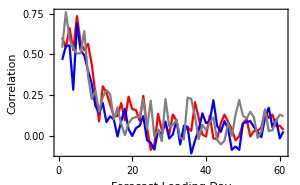
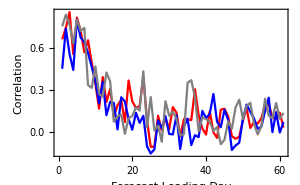
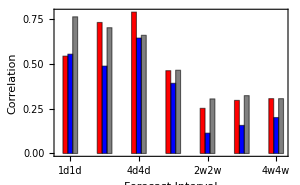
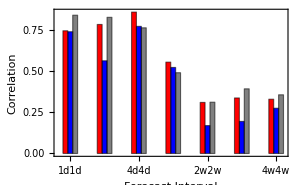
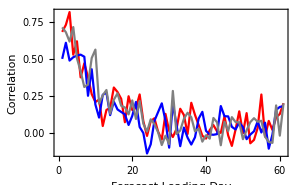
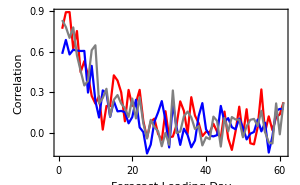
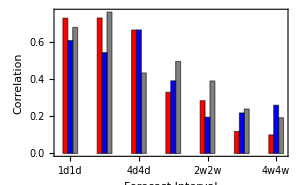
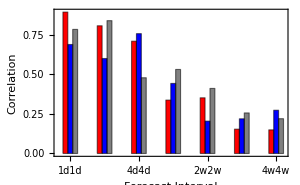
| Grid Daily Scale | Regional Daily Scale | Grid Interval Scale | Regional Interval Scale
SCA | -Graphics- | -Graphics- | -Graphics- | -Graphics-
NCA | -Graphics- | -Graphics- | -Graphics- | -Graphics-
OR | -Graphics- | -Graphics- | -Graphics- | -Graphics-
WA | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Visualize["MeteoFrance"]
```

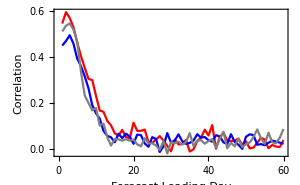
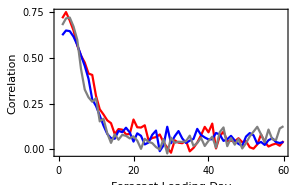
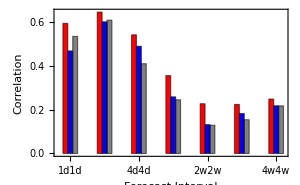
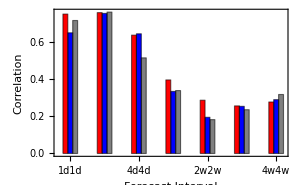
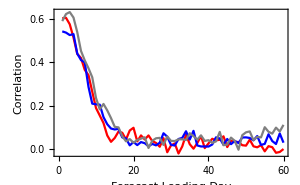
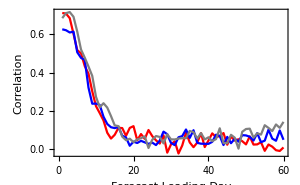
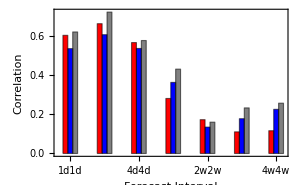
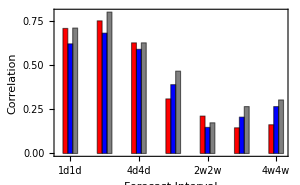
| Grid Daily Scale | Regional Daily Scale | Grid Interval Scale | Regional Interval Scale
SCA | -Graphics- | -Graphics- | -Graphics- | -Graphics-
NCA | -Graphics- | -Graphics- | -Graphics- | -Graphics-
OR | -Graphics- | -Graphics- | -Graphics- | -Graphics-
WA | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Visualize["CMA"]
```

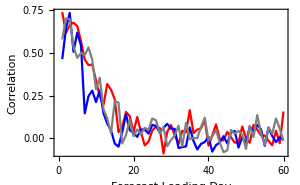
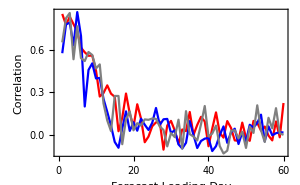
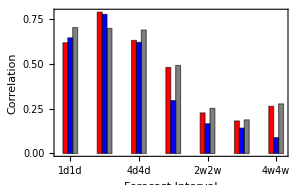
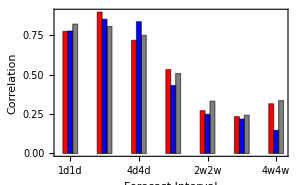
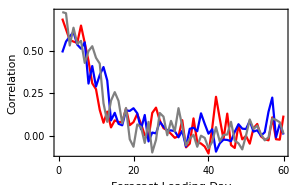
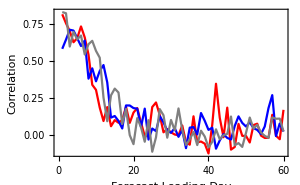
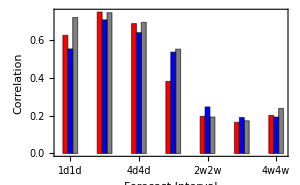
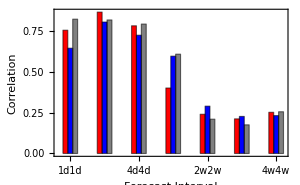
| Grid Daily Scale | Regional Daily Scale | Grid Interval Scale | Regional Interval Scale
SCA | -Graphics- | -Graphics- | -Graphics- | -Graphics-
NCA | -Graphics- | -Graphics- | -Graphics- | -Graphics-
OR | -Graphics- | -Graphics- | -Graphics- | -Graphics-
WA | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Visualize["UKMO"]
```

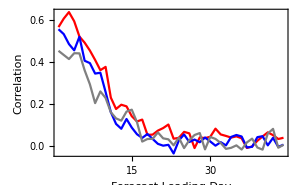
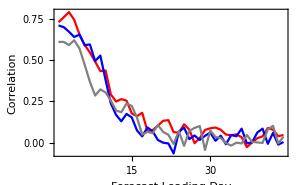
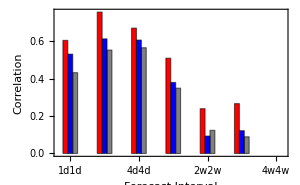
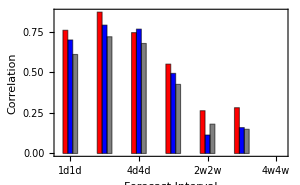
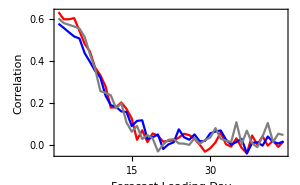
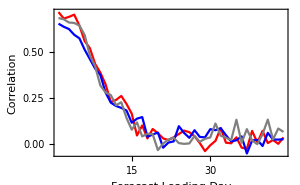
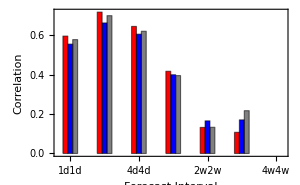
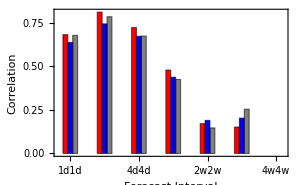
| Grid Daily Scale | Regional Daily Scale | Grid Interval Scale | Regional Interval Scale
SCA | -Graphics- | -Graphics- | -Graphics- | -Graphics-
NCA | -Graphics- | -Graphics- | -Graphics- | -Graphics-
OR | -Graphics- | -Graphics- | -Graphics- | -Graphics-
WA | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Visualize["NCEP"]
```

## Conclusion

The quite revolution of numerical prediction has brought

The quiet revolution of numerical weather models has been boosting a consistent increase in accuracy and extension of weather predictions. The progress require keeping clarifying the boundary between weather and climate.  
Extratropical cyclones, storm tracks.

there is never a sharp distincion